## Distributed Consensus Problem -- Testing

From: https://writings.stephenwolfram.com/2021/05/the-problem-of-distributed-consensus/

#### From The Webpage:

## A simple Distributive Consensus problem : with 3 colours

```mathematica
BlockRandom[SeedRandom[77]; (*create randomly 77 seeds*)
redd = Hue[0.15,0.72,1];
yelloww = Hue[0.98,1,0.8200000000000001];
bluee = Hue[0.60,1,0.8200000000000001];
initstate = Module[{pts=RandomPointConfiguration[HardcorePointProcess[0.10,2,2],Rectangle[{0,0},{50,50}]]["Points"],clrs}, (*setting the points parameters*)clrs=Table[RandomChoice[{.45,.35,.25 }->{redd,yelloww, bluee}],Length[pts]]; (*represents a color in the HSB color space with hue h, saturation & brightness*)
Graphics[{EdgeForm[Gray],Table[Style[Disk[pts[[n]]],clrs[[n]]],{n,Range[Length[pts]]}]}]]]
(*showing the Graphics from the parameters above*)
```

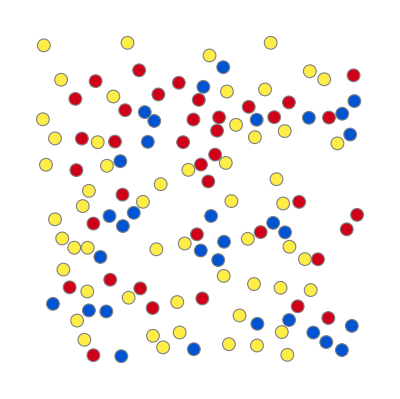

to efficiently find the most common colour among the nodes / finding the majority of the colour: 
First connect each node to some number of neighbors, picking the neighbors according to the spatial layout of the nodes:

```mathematica
ConsensusState[points_, colors_, nn_ : 5] := 
 NearestNeighborGraph[points, nn, DirectedEdges -> True, 
  DistanceFunction -> EuclideanDistance, 
  VertexStyle -> MapThread[Rule, {points, colors}], 
  VertexSize -> 0.75, EdgeStyle -> Black]; 
(*above defines a function*)

BlockRandom[SeedRandom[100]; 
Module[{pts=RandomPointConfiguration[HardcorePointProcess[0.10,2,2],Rectangle[{0,0},{50,50}]]["Points"],clrs}, (*setting the points parameters*)clrs=Table[RandomChoice[{.45,.35,.25 }->{redd,yelloww, bluee}],Length[pts]]; 
  ConsensusState[pts, clrs]]]
```

at each step updating the color of each node to be whatever the “majority color” of its neighbors is 
--> 	converges after a few steps to make all nodes have the “majority color” (which here is yellow)—or in effect 	“agree” on what the majority color is:

### Trial 1: 8 nearest neighbours (nn), 20 repeats, RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}], 100 seed random

```mathematica
ConsensusState[points_,colors_,nn_:8]:=NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance,VertexStyle->MapThread[Rule,{points,colors}],VertexSize->0.75,EdgeStyle->Black];
NodeDependencies[points_,nn_:8]:=Table[n->Flatten[Map[Position[points,#]&,VertexOutComponent[NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance],points[[n]],{1}]]],{n,Range[Length[points]]}]
SynchronousStepNewColors[dependencies_,colors_]:=Flatten[Map[With[{neighbors=Sort[Counts[Part[colors,Last[#]]],Greater]},If[DuplicateFreeQ[Values[neighbors]],First[Keys[neighbors]],colors[[First[#]]]]]&,dependencies]]
GraphicsGrid[Partition[BlockRandom[SeedRandom[100];Module[{pts=RandomPointConfiguration[HardcorePointProcess[0.09,2,2],Rectangle[{0,0},{50,50}]]["Points"],clrslist,highlights},clrslist=NestList[SynchronousStepNewColors[NodeDependencies[pts],#]&,Table[RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}],Length[pts]],20];
MapIndexed[With[{colors=#},Graph[ConsensusState[pts,colors],ImageSize->300]]&,clrslist]]],5],ImageSize->1700]
```

### Trial 2: 5 nearest neighbours (nn), 15 repeats, RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}]

```mathematica
ConsensusState[points_,colors_,nn_:5]:=NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance,VertexStyle->MapThread[Rule,{points,colors}],VertexSize->0.75,EdgeStyle->Black];
NodeDependencies[points_,nn_:5]:=Table[n->Flatten[Map[Position[points,#]&,VertexOutComponent[NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance],points[[n]],{1}]]],{n,Range[Length[points]]}]
SynchronousStepNewColors[dependencies_,colors_]:=Flatten[Map[With[{neighbors=Sort[Counts[Part[colors,Last[#]]],Greater]},If[DuplicateFreeQ[Values[neighbors]],First[Keys[neighbors]],colors[[First[#]]]]]&,dependencies]]
GraphicsGrid[Partition[BlockRandom[SeedRandom[100];Module[{pts=RandomPointConfiguration[HardcorePointProcess[0.09,2,2],Rectangle[{0,0},{50,50}]]["Points"],clrslist,highlights},clrslist=NestList[SynchronousStepNewColors[NodeDependencies[pts],#]&,Table[RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}],Length[pts]],20];
MapIndexed[With[{colors=#},Graph[ConsensusState[pts,colors],ImageSize->300]]&,clrslist]]],5],ImageSize->1700]
```

### Trial 3: 10 nearest neighbours (nn), 15 repeats, RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}]

```mathematica
ConsensusState[points_,colors_,nn_:10]:=NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance,VertexStyle->MapThread[Rule,{points,colors}],VertexSize->0.75,EdgeStyle->Black];
NodeDependencies[points_,nn_:10]:=Table[n->Flatten[Map[Position[points,#]&,VertexOutComponent[NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance],points[[n]],{1}]]],{n,Range[Length[points]]}]
SynchronousStepNewColors[dependencies_,colors_]:=Flatten[Map[With[{neighbors=Sort[Counts[Part[colors,Last[#]]],Greater]},If[DuplicateFreeQ[Values[neighbors]],First[Keys[neighbors]],colors[[First[#]]]]]&,dependencies]]
GraphicsGrid[Partition[BlockRandom[SeedRandom[100];Module[{pts=RandomPointConfiguration[HardcorePointProcess[0.09,2,2],Rectangle[{0,0},{50,50}]]["Points"],clrslist,highlights},clrslist=NestList[SynchronousStepNewColors[NodeDependencies[pts],#]&,Table[RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}],Length[pts]],20];
MapIndexed[With[{colors=#},Graph[ConsensusState[pts,colors],ImageSize->300]]&,clrslist]]],5],ImageSize->1700]
```

### Trial 4: 20 nearest neighbours (nn), 15 repeats, RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}]

```mathematica
ConsensusState[points_,colors_,nn_:10]:=NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance,VertexStyle->MapThread[Rule,{points,colors}],VertexSize->0.75,EdgeStyle->Black];
NodeDependencies[points_,nn_:10]:=Table[n->Flatten[Map[Position[points,#]&,VertexOutComponent[NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance],points[[n]],{1}]]],{n,Range[Length[points]]}]
SynchronousStepNewColors[dependencies_,colors_]:=Flatten[Map[With[{neighbors=Sort[Counts[Part[colors,Last[#]]],Greater]},If[DuplicateFreeQ[Values[neighbors]],First[Keys[neighbors]],colors[[First[#]]]]]&,dependencies]]
GraphicsGrid[Partition[BlockRandom[SeedRandom[100];Module[{pts=RandomPointConfiguration[HardcorePointProcess[0.09,2,2],Rectangle[{0,0},{50,50}]]["Points"],clrslist,highlights},clrslist=NestList[SynchronousStepNewColors[NodeDependencies[pts],#]&,Table[RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}],Length[pts]],20];
MapIndexed[With[{colors=#},Graph[ConsensusState[pts,colors],ImageSize->300]]&,clrslist]]],5],ImageSize->1700]
```

### Trial 5: 20 nearest neighbours (nn), 40 repeats, RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}]

```mathematica
ConsensusState[points_,colors_,nn_:10]:=NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance,VertexStyle->MapThread[Rule,{points,colors}],VertexSize->0.75,EdgeStyle->Black];
NodeDependencies[points_,nn_:10]:=Table[n->Flatten[Map[Position[points,#]&,VertexOutComponent[NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance],points[[n]],{1}]]],{n,Range[Length[points]]}]
SynchronousStepNewColors[dependencies_,colors_]:=Flatten[Map[With[{neighbors=Sort[Counts[Part[colors,Last[#]]],Greater]},If[DuplicateFreeQ[Values[neighbors]],First[Keys[neighbors]],colors[[First[#]]]]]&,dependencies]]
GraphicsGrid[Partition[BlockRandom[SeedRandom[100];Module[{pts=RandomPointConfiguration[HardcorePointProcess[0.09,2,2],Rectangle[{0,0},{50,50}]]["Points"],clrslist,highlights},clrslist=NestList[SynchronousStepNewColors[NodeDependencies[pts],#]&,Table[RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}],Length[pts]],40];
MapIndexed[With[{colors=#},Graph[ConsensusState[pts,colors],ImageSize->300]]&,clrslist]]],5],ImageSize->1700]
```

### Trial 6: 40 nearest neighbours (nn), 40 repeats, RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}]

```mathematica
ConsensusState[points_,colors_,nn_:40]:=NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance,VertexStyle->MapThread[Rule,{points,colors}],VertexSize->0.75,EdgeStyle->Black];
NodeDependencies[points_,nn_:40]:=Table[n->Flatten[Map[Position[points,#]&,VertexOutComponent[NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance],points[[n]],{1}]]],{n,Range[Length[points]]}]
SynchronousStepNewColors[dependencies_,colors_]:=Flatten[Map[With[{neighbors=Sort[Counts[Part[colors,Last[#]]],Greater]},If[DuplicateFreeQ[Values[neighbors]],First[Keys[neighbors]],colors[[First[#]]]]]&,dependencies]]
GraphicsGrid[Partition[BlockRandom[SeedRandom[100];Module[{pts=RandomPointConfiguration[HardcorePointProcess[0.09,2,2],Rectangle[{0,0},{50,50}]]["Points"],clrslist,highlights},clrslist=NestList[SynchronousStepNewColors[NodeDependencies[pts],#]&,Table[RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}],Length[pts]],40];
MapIndexed[With[{colors=#},Graph[ConsensusState[pts,colors],ImageSize->300]]&,clrslist]]],5],ImageSize->1700]
```

### Trial 7: 30 nearest neighbours (nn), 40 repeats, RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}]

```mathematica
ConsensusState[points_,colors_,nn_:30]:=NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance,VertexStyle->MapThread[Rule,{points,colors}],VertexSize->0.75,EdgeStyle->Black];
NodeDependencies[points_,nn_:30]:=Table[n->Flatten[Map[Position[points,#]&,VertexOutComponent[NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance],points[[n]],{1}]]],{n,Range[Length[points]]}]
SynchronousStepNewColors[dependencies_,colors_]:=Flatten[Map[With[{neighbors=Sort[Counts[Part[colors,Last[#]]],Greater]},If[DuplicateFreeQ[Values[neighbors]],First[Keys[neighbors]],colors[[First[#]]]]]&,dependencies]]
GraphicsGrid[Partition[BlockRandom[SeedRandom[100];Module[{pts=RandomPointConfiguration[HardcorePointProcess[0.09,2,2],Rectangle[{0,0},{50,50}]]["Points"],clrslist,highlights},clrslist=NestList[SynchronousStepNewColors[NodeDependencies[pts],#]&,Table[RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}],Length[pts]],40];
MapIndexed[With[{colors=#},Graph[ConsensusState[pts,colors],ImageSize->300]]&,clrslist]]],5],ImageSize->1700]
```

### 25 nearest neighbours (nn), 40 repeats, RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}]

```mathematica
ConsensusState[points_,colors_,nn_:25]:=NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance,VertexStyle->MapThread[Rule,{points,colors}],VertexSize->0.75,EdgeStyle->Black];
NodeDependencies[points_,nn_:25]:=Table[n->Flatten[Map[Position[points,#]&,VertexOutComponent[NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance],points[[n]],{1}]]],{n,Range[Length[points]]}]
SynchronousStepNewColors[dependencies_,colors_]:=Flatten[Map[With[{neighbors=Sort[Counts[Part[colors,Last[#]]],Greater]},If[DuplicateFreeQ[Values[neighbors]],First[Keys[neighbors]],colors[[First[#]]]]]&,dependencies]]
GraphicsGrid[Partition[BlockRandom[SeedRandom[100];Module[{pts=RandomPointConfiguration[HardcorePointProcess[0.09,2,2],Rectangle[{0,0},{50,50}]]["Points"],clrslist,highlights},clrslist=NestList[SynchronousStepNewColors[NodeDependencies[pts],#]&,Table[RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}],Length[pts]],40];
MapIndexed[With[{colors=#},Graph[ConsensusState[pts,colors],ImageSize->300]]&,clrslist]]],5],ImageSize->1700]
```

$Aborted

### looping from 5 to 25 in steps of 1 (nn), 5 repeats, RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}]

```mathematica
Do[Print["Trial ",nn]
ConsensusState[points_,colors_]:=NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance,VertexStyle->MapThread[Rule,{points,colors}],VertexSize->0.75,EdgeStyle->Black];
NodeDependencies[points_]:=Table[n->Flatten[Map[Position[points,#]&,VertexOutComponent[NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance],points[[n]],{1}]]],{n,Range[Length[points]]}]
SynchronousStepNewColors[dependencies_,colors_]:=Flatten[Map[With[{neighbors=Sort[Counts[Part[colors,Last[#]]],Greater]},If[DuplicateFreeQ[Values[neighbors]],First[Keys[neighbors]],colors[[First[#]]]]]&,dependencies]]
GraphicsGrid[Partition[BlockRandom[SeedRandom[100];Module[{pts=RandomPointConfiguration[HardcorePointProcess[0.09,2,2],Rectangle[{0,0},{50,50}]]["Points"],clrslist,highlights},clrslist=NestList[SynchronousStepNewColors[NodeDependencies[pts],#]&,Table[RandomChoice[{.45,.35,.25 }->{Red, Yellow, Blue}],Length[pts]],10];
MapIndexed[With[{colors=#},Graph[ConsensusState[pts,colors],ImageSize->300]]&,clrslist]]],5],ImageSize->1700],{nn,5,25,1}]
```

Trial 5

MapThread::mptd: Object points_ at position {2, 1} in MapThread[Rule,{points_,colors_}] has only 0 of required 1 dimensions.

NearestNeighborGraph::list: List expected at position 1 in NearestNeighborGraph[points_,5,DirectedEdges→True,DistanceFunction→EuclideanDistance,VertexStyle→MapThread[Rule,{points_,colors_}],VertexSize→0.75,EdgeStyle→GrayLevel[0]].

SetDelayed::write: Tag Times in Null NearestNeighborGraph[points_,5,DirectedEdges→True,DistanceFunction→EuclideanDistance,VertexStyle→MapThread[Rule,{points_,colors_}],VertexSize→0.75,EdgeStyle→GrayLevel[0]] is Protected.

Trial 6

MapThread::mptd: Object points_ at position {2, 1} in MapThread[Rule,{points_,colors_}] has only 0 of required 1 dimensions.

NearestNeighborGraph::list: List expected at position 1 in NearestNeighborGraph[points_,6,DirectedEdges→True,DistanceFunction→EuclideanDistance,VertexStyle→MapThread[Rule,{points_,colors_}],VertexSize→0.75,EdgeStyle→GrayLevel[0]].

SetDelayed::write: Tag Times in Null NearestNeighborGraph[points_,6,DirectedEdges→True,DistanceFunction→EuclideanDistance,VertexStyle→MapThread[Rule,{points_,colors_}],VertexSize→0.75,EdgeStyle→GrayLevel[0]] is Protected.

Trial 7

MapThread::mptd: Object points_ at position {2, 1} in MapThread[Rule,{points_,colors_}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

NearestNeighborGraph::list: List expected at position 1 in NearestNeighborGraph[points_,7,DirectedEdges→True,DistanceFunction→EuclideanDistance,VertexStyle→MapThread[Rule,{points_,colors_}],VertexSize→0.75,EdgeStyle→GrayLevel[0]].

General::stop: Further output of NearestNeighborGraph::list will be suppressed during this calculation.

SetDelayed::write: Tag Times in Null NearestNeighborGraph[points_,7,DirectedEdges→True,DistanceFunction→EuclideanDistance,VertexStyle→MapThread[Rule,{points_,colors_}],VertexSize→0.75,EdgeStyle→GrayLevel[0]] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

Trial 8

Trial 9

Trial 10

Trial 11

Trial 12

Trial 13

Trial 14

Trial 15

Trial 16

Trial 17

Trial 18

Trial 19

Trial 20

Trial 21

Trial 22

Trial 23

Trial 24

Trial 25